DEVBIO 232 Homework 2

February 15th, 2019
Samuel Morabito

#### Problem 1: Model negative, positive, and no autoregulation

## -Graphics-

```mathematica
ClearAll["Global`*"]
```

```mathematica
noAutoreg = {
Y'[t] == p -r Y[t], Y[0] == Yzero
};

posAutoreg = {
Y'[t] == p (Y[t]/(k + Y[t])) -r Y[t], Y[0] == Yzero
};
negAutoreg = {
Y'[t] == p (k/(k + Y[t])) -r Y[t], Y[0] == Yzero
};

(* define parameters for these ODEs*)
noParams = {p-> 1, Yzero-> 0, r-> 1};
negParams = {p-> 1, Yzero -> 0, r-> 0.5, k->1};
posParams = {p->4, Yzero-> 0.01, r->2, k->1};

(* replace symbols with parameter values for each ODE *)
noCase = noAutoreg /. noParams;
negCase = negAutoreg /. negParams;
posCase = posAutoreg /. posParams;

(* use NDSolve to get the numerical solution to these ODEs *)
solNoAutoreg = NDSolve[noCase, Y[t], {t, 0, 10}];
solNegAutoreg = NDSolve[negCase, Y[t], {t, 0, 10}];
solPosAutoreg = NDSolve[posCase, Y[t], {t, 0, 10}];
```

```mathematica
(* plot the solutions *)
Plot[{Y[t] /. solNoAutoreg, Y[t]/.solNegAutoreg, Y[t]/.solPosAutoreg}, {t, 0, 10}, AxesLabel-> {"t", "Y[t]"}, GridLines-> Automatic, PlotLegends-> {"no autoregulation", "- autoregulation", "+ autoregulation"}]
```

#### Problem 2: Cascades

2a: Model one or the other of these below cascades:

```mathematica
ClearAll["Global`*"]
```

```mathematica
xPrime = Piecewise[{{Y[t]/.solPosAutoreg, t > 0}, {1, t<0}}];
(*need to find thresh time based on when the previous function is at the thresh value*)
```

```mathematica
Plot[xPrime, {t, 1, 10}]
```

```mathematica
Y[t]/.solPosAutoreg
```

#### Problem 8: Lambda repressor system

A. Make a working model of the cI-cro double negative feedback loop. Note that cro is known to repress cI hyperbolically, so your model should reflect this. For cI repression of cro, use a biologically unrealistic Hill number of 10 in your input function. Your toy model should not include cI dimerization, assume cI acts as a monomer. Attempt to show that a small change in the starting amount of cI (the initial condition) will flip the steady state of the system from cro high, cI low, to cro low, cI high  (This will involve calling the Table function to get a dose-response curve where the ‘dose’ is the starting amount of cI; see the ‘Autoregulation_Demo’, ‘Gene_Networks-X_regulates_Y’ and/or ‘Positive_Autoregulation-Demonstrating_Bistability’ notebooks for examples).

ClearAll["Global`*"]
(* Define the system described in problem A *)
system1 = {
Y'[t] == P* k^n/(k^n + X[t]^n) -r*Y[t],(* Y = lambda repressor cI *)
X'[t] == P* k^n/(k^n + Y[t]^n) -r*X[t], (* X = cro *)
 Y[0] == Yzero,X[0] == Xzero
};

(* Numerically solve the system *) 
params1 = {P → 10, k→ 5, r→ 1, n→ 1, Yzero→10, Xzero→ 0};
solution1 = NDSolve[system1 /. params1, {Y[t], X[t]}, {t,0,20}] ;

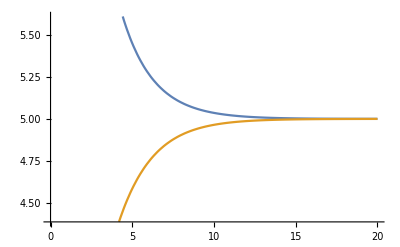

```mathematica
Plot[{Y[t] /. solution1, X[t] /. solution1}, {t,0,20}]
```

```mathematica
Manipulate[params1 = {P-> PValue, k-> kValue, r-> rValue, n-> nValue, Yzero-> YzeroValue, Xzero-> XzeroValue};
sol1 =  NDSolve[system1 /. params1, {Y[t], X[t]}, {t,0,20}] ;
Plot[{Y[t] /. sol1, X[t] /. sol1}, {t, 0,20}, PlotRange->{0,10}, AxesLabel-> {"time", "concentration"}],
{{PValue,10},1,10, Appearance-> "Labeled"},
{{kValue, 1}, 0.1, 10, Appearance-> "Labeled"},
{{nValue, 1}, 1, 100, Appearance -> "Labeled"},
{{YzeroValue,10},0,50, Appearance-> "Labeled"},
{{XzeroValue,0}, 0, 50, Appearance -> "Labeled"},
{{rValue, 1}, 0.1, 10, Appearance-> "Labeled"}
]
```

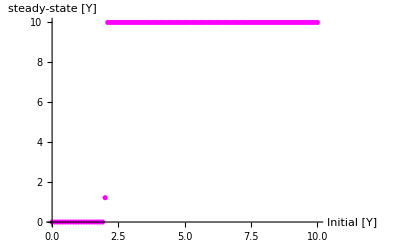

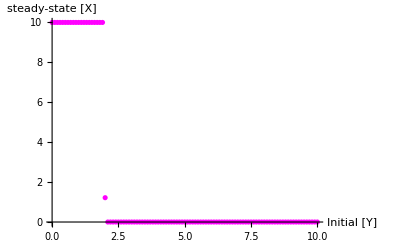

```mathematica
(* Show bistability? *)
(* k must be less than half of P for bistability to work *)

params1 = {P -> 10, k-> 1, r-> 1, n-> 10, Yzero->i, Xzero-> 2};
table1 = Table[{i, Y[t] /. Flatten[NDSolve[system1 /. params1, {Y[t]}, {t,0,20}]] /. t-> 20 }, {i, 0, 10, 0.1}];
table2 = Table[{i, X[t] /. Flatten[NDSolve[system1 /. params1, {X[t]}, {t,0,20}]] /. t-> 20 }, {i, 0, 10, 0.1}];
ListPlot[table1, PlotRange-> All, PlotStyle-> {Magenta, Thick}, AxesLabel-> {"Initial [Y]", "steady-state [Y]" }]
ListPlot[table2, PlotRange-> All, PlotStyle-> {Magenta, Thick}, AxesLabel-> {"Initial [Y]", "steady-state [X]" }]
```

B. How does your model in A behave if there is no cooperativity, i.e. if the Hill number for cI repression of cro is 1?  How does your model in A behave if you use a Hill number of 2, which approximates experimental measurements?

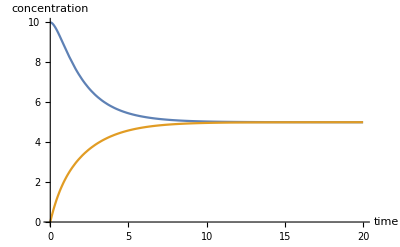

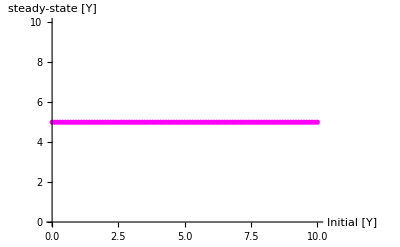

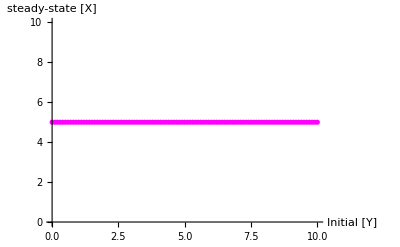

```mathematica
(* Hill number n = 1*)
params1 = {P -> 10, k-> 5, r-> 1, n-> 1, Yzero->10, Xzero-> 0};
solution1 = NDSolve[system1 /. params1, {Y[t], X[t]}, {t,0,20}] ;                       
Plot[{Y[t] /. solution1, X[t] /. solution1}, {t,0,20} ,PlotRange->{0,10}, AxesLabel-> {"time", "concentration"}]

params1 = {P -> 10, k-> 5, r-> 1, n-> 1, Yzero->i, Xzero-> 2};
table1 = Table[{i, Y[t] /. Flatten[NDSolve[system1 /. params1, {Y[t]}, {t,0,20}]] /. t-> 20 }, {i, 0, 10, 0.1}];
table2 = Table[{i, X[t] /. Flatten[NDSolve[system1 /. params1, {X[t]}, {t,0,20}]] /. t-> 20 }, {i, 0, 10, 0.1}];
ListPlot[table1, PlotRange-> {0,10}, PlotStyle-> {Magenta, Thick}, AxesLabel-> {"Initial [Y]", "steady-state [Y]" }]
ListPlot[table2, PlotRange-> {0,10}, PlotStyle-> {Magenta, Thick}, AxesLabel-> {"Initial [Y]", "steady-state [X]" }]
```

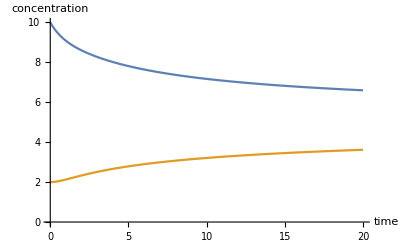

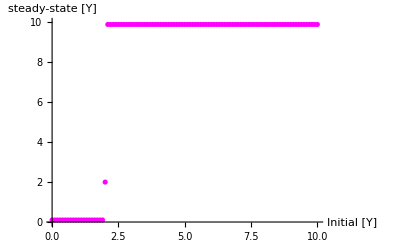

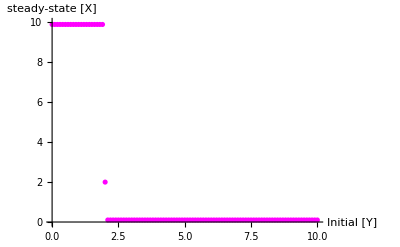

```mathematica
(* Hill number n = 2 *)
params1 = {P -> 10, k-> 5, r-> 1, n-> 2, Yzero->10, Xzero-> 2};
solution1 = NDSolve[system1 /. params1, {Y[t], X[t]}, {t,0,20}] ;                       
Plot[{Y[t] /. solution1, X[t] /. solution1}, {t,0,20} ,PlotRange->{0,10}, AxesLabel-> {"time", "concentration"}]

params1 = {P -> 10, k-> 1, r-> 1, n-> 2, Yzero->i, Xzero-> 2};
table1 = Table[{i, Y[t] /. Flatten[NDSolve[system1 /. params1, {Y[t]}, {t,0,20}]] /. t-> 20 }, {i, 0, 10, 0.1}];
table2 = Table[{i, X[t] /. Flatten[NDSolve[system1 /. params1, {X[t]}, {t,0,20}]] /. t-> 20 }, {i, 0, 10, 0.1}];
ListPlot[table1, PlotRange-> {0,10}, PlotStyle-> {Magenta, Thick}, AxesLabel-> {"Initial [Y]", "steady-state [Y]" }]
ListPlot[table2, PlotRange-> {0,10}, PlotStyle-> {Magenta, Thick}, AxesLabel-> {"Initial [Y]", "steady-state [X]" }]
```

C. Now add the fact the cI also positively autoregulates itself to the toy model you designed in A.  
	The proper logic for transcription from the cI promoter is “cI AND NOT cro”.  That is, cI needs to be bound (it’s an activator), and cro can’t be bound (it’s a repressor).  Note the similarity of this logic to the logic for the lac operon.
	For cI repression of cro, again use a Hill number of 2. You should use the same Hill number (i.e. 2) for the part of the input function that describes the positive autoregulation. Again, you should attempt to show that a small change in the starting amount of cI (i.e. the initial condition) will flip the steady-state system from cro high, cI low to cro low, cI high.

```mathematica
system2 = {
Y'[t] == P* k^n/(k^n + X[t]^n) * Y[t]^n/(k^n + Y[t]^n)-r*Y[t] ,(* Y = lambda repressor cI *)
X'[t] == P* k^n/(k^n + Y[t]^n) -r*X[t], (* X = cro *)
 Y[0] == Yzero,X[0] == Xzero
};

(* Numerically solve the system *) 
params2 = {P -> 10, k-> 5, r-> 1, n-> 10, Yzero->10, Xzero-> 2};
solution2 = NDSolve[system2 /. params2, {Y[t], X[t]}, {t,0,20}] ;
```

```mathematica
Manipulate[params2 = {P-> PValue, k-> kValue, r-> rValue, n-> nValue, Yzero-> YzeroValue, Xzero-> XzeroValue};
sol2 =  NDSolve[system2 /. params2, {Y[t], X[t]}, {t,0,20}] ;
Plot[{Y[t] /. sol2, X[t] /. sol2}, {t, 0,20}, PlotRange->{0,21}, AxesLabel-> {"time", "concentration"}],
{{PValue,10},1,10, Appearance-> "Labeled"},
{{kValue, 1}, 0.1, 10, Appearance-> "Labeled"},
{{nValue, 1}, 1, 100, Appearance -> "Labeled"},
{{YzeroValue,10},0,50, Appearance-> "Labeled"},
{{XzeroValue,0}, 0, 50, Appearance -> "Labeled"},
{{rValue, 1}, 0.1, 10, Appearance-> "Labeled"}
]
```

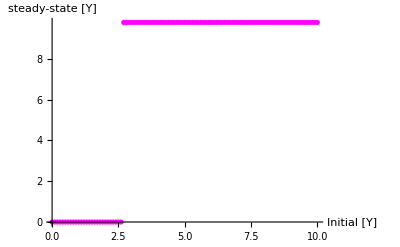

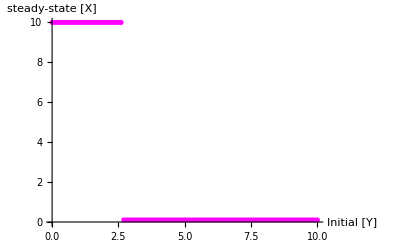

```mathematica
params2 = {P -> 10, k-> 1, r-> 1, n-> 2, Yzero->i, Xzero-> 2};
table1 = Table[{i, Y[t] /. Flatten[NDSolve[system2 /. params2, {Y[t]}, {t,0,20}]] /. t-> 20 }, {i, 0, 10, 0.1}];
table2 = Table[{i, X[t] /. Flatten[NDSolve[system2 /. params2, {X[t]}, {t,0,20}]] /. t-> 20 }, {i, 0, 10, 0.1}];
ListPlot[table1, PlotRange-> All, PlotStyle-> {Magenta, Thick}, AxesLabel-> {"Initial [Y]", "steady-state [Y]" }]
ListPlot[table2, PlotRange-> All, PlotStyle-> {Magenta, Thick}, AxesLabel-> {"Initial [Y]", "steady-state [X]" }]
```

D. How does your model in C behave if there is no cooperativity, i.e.if all Hill numbers are 1?

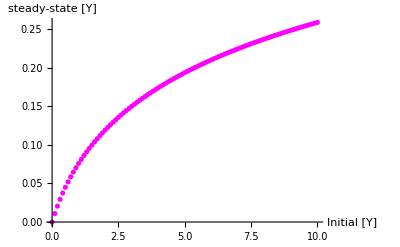

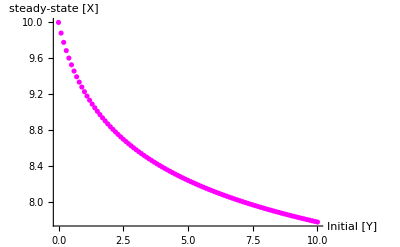

```mathematica
params2 = {P -> 10, k-> 1, r-> 1, n-> 1, Yzero->i, Xzero-> 15};
table1 = Table[{i, Y[t] /. Flatten[NDSolve[system2 /. params2, {Y[t]}, {t,0,20}]] /. t-> 20 }, {i, 0, 10, 0.1}];
table2 = Table[{i, X[t] /. Flatten[NDSolve[system2 /. params2, {X[t]}, {t,0,20}]] /. t-> 20 }, {i, 0, 10, 0.1}];
ListPlot[table1, PlotRange-> All, PlotStyle-> {Magenta, Thick}, AxesLabel-> {"Initial [Y]", "steady-state [Y]" }]
ListPlot[table2, PlotRange-> All, PlotStyle-> {Magenta, Thick}, AxesLabel-> {"Initial [Y]", "steady-state [X]" }]
```